```mathematica
Clear["Global`*"]
(*Define Ouput Print Function*)
MyPrint[args__,{style__}]:=Print[Row[{args},BaseStyle->{style}]]
```

## Coefficient of the Kinetic Term

```mathematica
(*This is the Kähler Potential!
Fill in the arguments and define the function as you like, but don't change the name of the function "K" to something else. *)
K[Φ_,S_]:= Abs[Φ]^2+ Abs[Conjugate[Φ]]^2+Abs[S]^2

(*This is the Super Potential!
Fill in the arguments and define the function as you like, but don't change the name of the function "W" to something else. *)
W[Φ_ ,S_]:= S*(-μ^2+(Abs[Φ])^(2m)/M^(2(m-1)))

(*Set Conditions for Parameters in the above potentials to get refine results*)
ParameterConditions = {μ,M,m}∈Reals ;


argList[f_]:=ReleaseHold[DownValues[f][[1,1]]/.{f->List}][[All,1]];
Pot[f_]:=DownValues[f][[1,2]];
ComplexD[f_, i_] :=
ResourceFunction["ComplexD"][ DownValues[f][[1,2]],argList[f][[i]] ];
ComplexDD[f_, i_, j_] := ResourceFunction["ComplexD"][
ResourceFunction["ComplexD"][ DownValues[f][[1,2]],argList[f][[i]] ]
,Conjugate[argList[K][[j]]]
];

Numfields =Length[argList[K]];
(*Kij matrix*)
KijmatrixValue = Table[ 
ComplexDD[K, i, j],{i,1,Numfields},{j,1,Numfields}];

KijmatrixName =Table[ 
Subscript[K,argList[K][[i]]*OverBar[argList[K][[j]]]],{i,1,Numfields},{j,1,Numfields}];

(*DW vector*)
DWvectorValue = Table[ 
Simplify[ComplexD[W,i]+ComplexD[K,i]*Pot[W],ParameterConditions]
,{i,1,Numfields}];

DWvectorName = Table[Row[{Subscript[D,argList[K][[i]]],W}],{i,1,Numfields}];
(*OverBar[DW] vector*)
DWconjvectorValue = Table[ 
Simplify[Conjugate[ComplexD[W,i]+ComplexD[K,i]*Pot[W]],ParameterConditions],{i,1,Numfields}];

DWconjvectorName =Table[OverBar[Row[{Subscript[D,argList[K][[i]]],W}]],{i,1,Numfields}];

(*Fterm Potential*)
FtermPotential = Exp[Pot[K]]*(DWvectorValue.Inverse[KijmatrixValue].DWconjvectorValue-3Conjugate[Pot[W]]*Pot[W]);




(*Print Out Results*)
MyPrint["Kähler Potential:   ",TraditionalForm[Pot[K]],"\nNumber of fields: " ,Numfields ,",  Fields: ",argList[K],{"Subsection",FontColor->Blue}];
MyPrint["Coefficient matrix of the kinetic term:\n K_(i OverscriptBox[j, _]) = "
,MatrixForm[KijmatrixName]," = ",MatrixForm[KijmatrixValue],{"Subsection",FontColor->Blue}];
MyPrint["Inverse of coefficient matrix of the kinetic term:\n (K^-1)_(i OverscriptBox[j, _]) = ",MatrixForm[Inverse[KijmatrixValue]],{"Subsection",FontColor->Blue}];
MyPrint["Super Potential:   ",TraditionalForm[Pot[W]],{"Subsection",FontColor->Magenta}];
MyPrint[Row[{Subscript[D, Subscript[Φ, i]],W}]," = "
,MatrixForm[DWvectorName]," \n = ",TraditionalForm[MatrixForm[
Assuming[ParameterConditions,Refine[DWvectorValue]]
]],{"Subsection",FontColor->Red}];
MyPrint[OverBar[Row[{Subscript[D, Subscript[Φ, i]],W}]]," = "
,MatrixForm[DWconjvectorName]," \n = ",TraditionalForm[MatrixForm[
Assuming[ParameterConditions,Refine[DWconjvectorValue]]
]],{"Subsection",FontColor->Green}];
MyPrint[OverBar[Row[{Subscript[D, Subscript[Φ, i]],W}]]," = "
,MatrixForm[DWconjvectorName]," \n = ",TraditionalForm[MatrixForm[
DWconjvectorValue]]
,{"Subsection",FontColor->Green}];
MyPrint["Fterm Potential:   ",TraditionalForm[Replace[Assuming[ParameterConditions,Simplify[FtermPotential] ],
-μ^2+(Φ*Conjugate[Φ])^m/M^(2(m-1))-> a]],{"Subsection",FontColor->Black}];
```

Kähler Potential:   Abs[S]^2+2 Abs[Φ]^2
Number of fields: 2,  Fields: {Φ,S}

Coefficient matrix of the kinetic term:
 K_(i OverscriptBox[j, _]) = (K_(Φ Φ̄) | K_(Φ S̄)
K_(S Φ̄) | K_(S S̄)) = (2 | 0
0 | 1)

Inverse of coefficient matrix of the kinetic term:
 (K^-1)_(i OverscriptBox[j, _]) = (1/2 | 0
0 | 1)

Super Potential:   S (M^(-2 (m-1)) Abs[Φ]^(2 m)-μ^2)

D_Φ_iW = (D_ΦW
D_SW) 
 = (S Conjugate[Φ] (m M^(2-2 m) Abs[Φ]^(2 (m-1))+2 M^(2-2 m) Abs[Φ]^(2 m)-2 μ^2)
(S Conjugate[S]+1) M^(-2 m) (M^2 Abs[Φ]^(2 m)-μ^2 M^(2 m)))

OverBar[D_Φ_iW] = (OverBar[D_ΦW]
OverBar[D_SW]) 
 = (Φ (m Abs[Φ]^(2 m-2) Conjugate[(M^(2-2 m) S)]-2 Conjugate[S] (μ^2-Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))]))
(S Conjugate[S]+1) (-(μ^2-Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))])))

OverBar[D_Φ_iW] = (OverBar[D_ΦW]
OverBar[D_SW]) 
 = (Φ (Conjugate[(m M^(2-2 m) S Abs[Φ]^(2 m-2))]-2 Conjugate[S] (μ^2-Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))]))
(S Conjugate[S]+1) (-(μ^2-Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))])))

Fterm Potential:   ⅇ^(Abs[S]^2+2 Abs[Φ]^2) (-3 S Conjugate[S] (M^(2-2 m) Abs[Φ]^(2 m)-μ^2) (Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))]-μ^2)+1/2 S Φ Conjugate[Φ] (m M^(2-2 m) Abs[Φ]^(2 (m-1))+2 M^(2-2 m) Abs[Φ]^(2 m)-2 μ^2) (Conjugate[(m M^(2-2 m) S Abs[Φ]^(2 m-2))]-2 Conjugate[S] (μ^2-Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))]))+(S Conjugate[S]+1)^2 M^(-2 m) (M^2 Abs[Φ]^(2 m)-μ^2 M^(2 m)) (Abs[Φ]^(2 m) Conjugate[(M^(2-2 m))]-μ^2))

```mathematica
Wterm =-μ^2+(Φ*Conjugate[Φ])^m/M^(2(m-1))
Conjugate[Wterm]
Replace[Wterm^2 ,-μ^2+(Φ*Conjugate[Φ])^m/M^(2(m-1))-> a,{2}]
```

-μ^2+M^(-2 (-1+m)) (Φ Conjugate[Φ])^m

-Conjugate[μ]^2+Conjugate[M^(-2 (-1+m)) (Φ Conjugate[Φ])^m]

(-μ^2+M^(-2 (-1+m)) (Φ Conjugate[Φ])^m)^2

```mathematica
ResourceFunction["ComplexD"][ (CN/4)*Abs[Phi]^4,Phi]
Simplify[ResourceFunction["ComplexD"][ ResourceFunction["ComplexD"][ (CN/4)*Abs[Phi]^4,Phi],Conjugate[Phi]]]
```

1/2 CN Abs[Phi]^2 Conjugate[Phi]

1/2 CN (Abs[Phi]^2+Phi Conjugate[Phi])

## Hybrid Inflation expansion

```mathematica
Clear["Global`*"];
A[ ψ_]:= -μ^2+(ψ/2)^(2m)/M^(2(m-1));
VHybrid[m_, σ_, ψ_]:=Exp[ σ^2/2+ψ^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(A[ ψ])^2+2*σ^2/2*(m/2^(2m-1)*ψ^(2m-1)/M^(2(m-1))+ψ/2*A[ ψ])^2);

m = 2;l=4;
Normal[Series[VHybrid[m, σ*t, ψ*t],{t,0,l}]]/. t->1;
VHybridwUpto[m_, l_] :=Normal[Series[VHybrid[m, σ*t, ψ*t],{t,0,l}]]/. t->1;

(*TeXForm[ VnewUpto[n , 6]]*)
VHybridwUpto[m , 4]
VHybridwUpto[m , 8]
```

μ^4+(μ^4 ψ^2)/2+(M^2 μ^4 σ^4+2 M^2 μ^4 σ^2 ψ^2-μ^2 ψ^4+M^2 μ^4 ψ^4)/(8 M^2)

μ^4+(μ^4 σ^4)/4+(μ^4 ψ^2)/2+1/4 μ^4 σ^2 ψ^2-(μ^2 ψ^4)/(8 M^2)-(3 μ^2 σ^2 ψ^4)/(16 M^2)-(μ^2 σ^4 ψ^4)/(32 M^2)-((-2+M^2 μ^2) σ^2 ψ^6)/(32 M^4)+ψ^8/(256 M^4)-1/4 μ^4 σ^2 (σ^2+ψ^2)-(3 μ^2 σ^2 ψ^4 (σ^2+ψ^2))/(32 M^2)+1/8 μ^4 (σ^2+ψ^2)^2-1/16 μ^4 σ^2 (σ^2+ψ^2)^2+1/48 μ^4 (σ^2+ψ^2)^3-1/96 μ^4 σ^2 (σ^2+ψ^2)^3+1/384 μ^4 (σ^2+ψ^2)^4+1/2 (σ^2+ψ^2) ((μ^4 σ^4)/4+1/4 μ^4 σ^2 ψ^2-(μ^2 ψ^4)/(8 M^2))+1/8 (σ^2+ψ^2)^2 ((μ^4 σ^4)/4+1/4 μ^4 σ^2 ψ^2-(μ^2 ψ^4)/(8 M^2))

```mathematica
μ=2.7*10^-3;M=1.6;m= 2;
A[ ψ_]:= -μ^2+(ψ/2)^(2m)/M^(2(m-1));
VHybridExact[σ_, ψ_]:=Exp[ σ^2/2+ψ^2/2]*((1- σ^2/2+ (σ^2/2)^2)*(A[ ψ])^2+2*σ^2/2*(m/2^(2m-1)*ψ^(2m-1)/M^(2(m-1))+ψ/2*A[ ψ])^2);
VHybridPRApprox[σ_, ψ_]:=( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M^(2m-2)))*(-μ^2+ ψ^(2m)/(4^m * M^(2m-2)) ) ;
VHybrid4thOrderExact[σ_, ψ_]:= ( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2+(σ^2*ψ^2)/4+ψ^4/8)+ ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) + ((m * ψ^(2m) * σ^2)/(2^(2m-1)*M^(2m-2)))*(-μ^2+ ψ^(2m)/(4^m * M^(2m-2)) ) ;
VHybridSimplest[σ_, ψ_]:=( -μ^2+ ψ^(2m)/(4^m*M^(2m-2)) )^2 * (1+σ^4/8+ψ^2/2) + ((m^2*σ^2*ψ^2)/4^(2m-1))*(ψ/M)^(4m-4) ;
{min,max}={0,6*10^-11};
HybridStyle = {ScalingFunctions->{"Reverse",None},PlotRange->{min,max}, AxesStyle->Directive[Black,FontSize->10],ColorFunction->(ColorData["SolarColors"][#3]&),ColorFunctionScaling->True,PlotLegends->BarLegend[{"SolarColors",{min,max}},LabelStyle->{Black}],Mesh -> 40, MeshStyle->Directive[Gray, Opacity[0.5]]};
Plot3D[VHybridExact[σ, ψ],{ψ,0,0.16},{σ,-0.2,0.8},Evaluate[HybridStyle]]
Plot3D[VHybridPRApprox[σ, ψ],{ψ,0,0.16},{σ,-0.2,0.8},Evaluate[HybridStyle]]

Plot3D[VHybrid4thOrderExact[σ, ψ],{ψ,0,0.16},{σ,-0.2,0.8},Evaluate[HybridStyle]]

Plot3D[VHybridSimplest[σ, ψ],{ψ,0,0.16},{σ,-0.2,0.8},Evaluate[HybridStyle]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## New Inflation expansion

```mathematica
Clear["Global`*"];
```

```mathematica
VNew[n_, ϕ_]:= Exp[ (ϕ/(√2))^2+CN/4*(ϕ/(√2))^4]/(1+CN *(ϕ/(√2))^2)*(((1+ (ϕ/(√2))^2+CN/2*(ϕ/(√2))^4)*v^2-(1+ (ϕ/(√2))^2/(n+1)+CN/2*(ϕ/(√2))^4/(n+1))*g*(ϕ/(√2))^n)^2-3*(1+CN*(ϕ/(√2))^2)*(ϕ/(√2))^2*(v^2-g/(n+1)*(ϕ/(√2))^n)^2);
VnewUpto[n_, l_] :=Series[VNew[n, ϕ],{ϕ,0,l}];
n = 6;
(*TeXForm[ VnewUpto[n , 6]]*)
VnewUpto[n , 6]
```

v^4-1/2 (CN v^4) ϕ^2+(v^4/4-1/2 (1/2-CN/2) v^4-(CN v^4)/2+(1/4 (1/2+CN/4)-CN/4+CN^2/4) v^4) ϕ^4+(-(g v^2)/4+(CN v^4)/8-1/2 (1/4 (1/2+CN/4)-CN/4+CN^2/4) v^4+(1/6 (1/4 (1/2+CN/4)+CN/8)-1/8 (1/2+CN/4) CN+CN^2/8-CN^3/8) v^4+(1/2-CN/2) (v^4/4-(CN v^4)/2)) ϕ^6+O[ϕ]^7

4.87968×10^-14-9.75936×10^-16 ϕ^2-2.209×10^-12 ϕ^4+2.5×10^-11 ϕ^16

4.87968×10^-14-9.75936×10^-16 ϕ^2-2.20373×10^-12 ϕ^4

0.324184

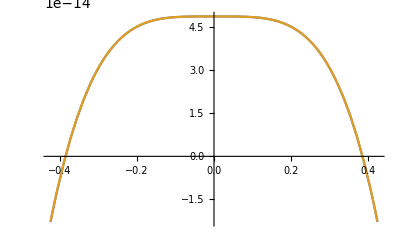

```mathematica
v = 4.7*10^(-4);
CN = 0.04;
g = 2.0*10^(-5);
VnewOrder2[ϕ_]:= v^4-1/2 (CN* v^4)* ϕ^2+1/16*(-8 *g* v^2) *ϕ^4+g^2/16*ϕ^16;
VnewOrder4[ϕ_]:= v^4-1/2 *(CN* v^4)* ϕ^2+1/16*(-8 *g* v^2+2 v^4-7 CN* v^4+4 CN^2 *v^4) *ϕ^4;
VnewOrder2[ϕ]
VnewOrder4[ϕ]
ϕmin = (v^2/g)^(1/n)
Plot[{VnewOrder2[ϕ],VnewOrder4[ϕ]},{ϕ,-ϕmin-0.1,ϕmin+0.1}]
```

```mathematica
Normal[Series[Exp[(x*t)^2/2+(y*t)^2/2],{t,0,4}]]/. t->1
```

1+1/2 (x^2+y^2)+1/8 (x^2+y^2)^2